# 量子搜索算法

## Quantum Search Algorithm

## 魏文杰

## 甲辰年正月廿二2024年3月2日22:53:32

```mathematica
<<Wolfram`QuantumFramework`
```

## 目录

简介：搜索问题的提法

布尔预言机和相位翻转预言机

Grover算法的流程

Grover算法的几何意义

例：Grover算法的成功概率

启发式推导

## 简介

量子搜索算法

1996  Grover 算法对非结构化搜索问题进行了量子二次加速

推广：振幅放大 amplitude amplification

量子计算机要想对精确组合优化产生影响，必须做到以下两点之一：1）量子硬件的预期底层时钟速度和容错量子计算的开销取得巨大进步；或 2）量子算法的开发大大超过Grover算法提供的四倍速度1。

### 搜索问题的提法

在无结构的N个物件中找到M个目标物件。

给被搜索的 N=2^n 个物件编号，假设存在一个预言机(oracle)能判断任意一个编号的东西是否为我们搜索的目标，f(x)=1表示是，f(x)=0表示否。

搜索算法的目标是尽可能少地调用预言机并找到问题的解。

量子版本的预言机是一个幺正变换
|x⟩|q⟩⟶^O|x⟩|q⊕f(x)⟩
-Graphics-
|x⟩⟶^O(-1)^(f(x))|x⟩

## 布尔预言机2

布尔预言机的作用由以下变换定义：xq->xq⊕f(x) ，其中 | x⟩ 是n个量子比特寄存器状态，q 是记录f(x)的计算结果的辅助比特

Define a Boolean function of 3-SAT with 5 clauses:
定义一个布尔函数

```mathematica
f=And[!v1||!v2||!v3,v1||!v2||v3,v1||v2||!v3,v1||!v2||!v3,!v1||v2||v3];
```

真值表:

```mathematica
ResourceFunction["TruthTable"][f,{v1,v2,v3}]
```

v1 | v2 | v3 | (!v1||!v2||!v3)&&(v1||!v2||v3)&&(v1||v2||!v3)&&(v1||!v2||!v3)&&(!v1||v2||v3)
True | True | True | False
True | True | False | True
True | False | True | True
True | False | False | False
False | True | True | False
False | True | False | False
False | False | True | False
False | False | False | True

相应的量子线路:

```mathematica
oracle=QuantumCircuitOperator[{"BooleanOracle",f}];
```

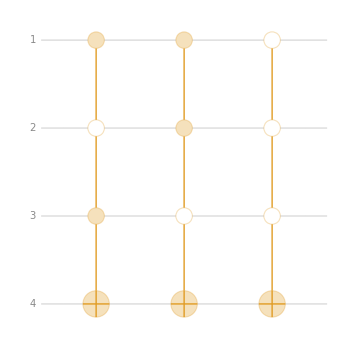

```mathematica
oracle["Diagram"]
```

第四个比特是辅助比特，初始化到零

We shall prepare the 4-qubit in above circuit (ie the ancillary qubit) is 0 state, and then other qubits (1-3) in the index register states. To compare with above truth table, we will create the index register states |x> in the order |2^n-1> down to |0>

```mathematica
states=QuantumTensorProduct[#,QuantumState["0"]]&/@Table[QuantumState[{"Register",3,i}],{i,2^3-1,0,-1}];
```

Create a list with elements {|x>,|q⊕f(x)}:
验证经典线路同量子线路实现相同的功能

```mathematica
TableForm[Transpose[{Table[QuantumState[{"Register",3,i}]["Formula"],{i,2^3-1,0,-1}],QuantumPartialTrace[oracle[#],{1,2,3}]["Formula"]&/@states}],TableHeadings->{None, {Ket[{x}],Ket[{q ⊕ HoldForm[f[x]]}]}}]
```

x | q⊕f[x]
111 | 0
110 | 1
101 | 1
100 | 0
011 | 0
010 | 0
001 | 0
000 | 1

如果将辅助比特制备到，那么预言机的作用将是在真输入的态前面加上负号

If the initial state of the ancillary qubit is |->, the overall effect of the oracle will be adding - sign in front of |x> with x the solution of Boolean function

```mathematica
states=QuantumTensorProduct[#,QuantumState["Minus"]]&/@Table[QuantumState[{"Register",3,i}],{i,2^3-1,0,-1}];
results=Transpose[{states,oracle/@states}];
TableForm[Transpose[{Table[QuantumState[{"Register",3,i}]["Formula"],{i,2^3-1,0,-1}],QuantumOperator[QuantumState["Minus"]["Dagger"],{4}][#]["Formula"]&/@oracle/@states}],TableHeadings->{None, {"|x>","oracle|x>"}}]
```

|x> | oracle|x>
111 | 111
110 | -110
101 | -101
100 | 100
011 | 011
010 | 010
001 | 001
000 | -000

## 相位翻转预言机

The action of a phase oracle can be defined as the following transformation:   with  the index register state of n-qubits,

Define a Boolean function of 3-SAT with 4 clauses:

```mathematica
f=And[!v1||!v2||!v3,v1||!v2||v3,v1||v2||!v3,v1||!v2||!v3];
```

Truth table of above Boolean function:

```mathematica
ResourceFunction["TruthTable"][f,{v1,v2,v3}]
```

v1 | v2 | v3 | (!v1||!v2||!v3)&&(v1||!v2||v3)&&(v1||v2||!v3)&&(v1||!v2||!v3)
True | True | True | False
True | True | False | True
True | False | True | True
True | False | False | True
False | True | True | False
False | True | False | False
False | False | True | False
False | False | False | True

Corresponding oracle’s quantum circuit:

```mathematica
phaseOracle=QuantumCircuitOperator[{"PhaseOracle",f}];
```

The diagram of oracle:

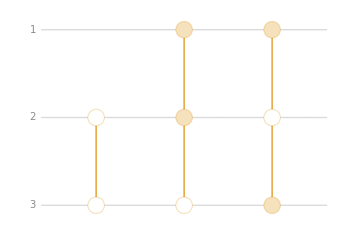

```mathematica
phaseOracle["Diagram"]
```

We shall prepare the 3-qubit in the index register states. To compare with above truth table, we will create the index register states |x> in the order |2^n-1> down to |0>

```mathematica
states=Table[QuantumState[{"Register",3,i}],{i,2^3-1,0,-1}];
```

Create a list with elements {|x>,(-1)^(f(x))|x>}:

```mathematica
TableForm[Transpose[{Table[QuantumState[{"Register",3,i}]["Formula"],{i,2^3-1,0,-1}],phaseOracle[#]["Formula"]&/@states}],TableHeadings->{None, {"|x>","(-1)^(f (x))|x>"}}]
```

|x> | (-1)^(f (x))|x>
111 | 111
110 | -110
101 | -101
100 | -100
011 | 011
010 | 010
001 | 001
000 | -000

## Grover算法

### 完整流程

-Graphics-

### Grover迭代：-Graphics-

-Graphics-

-Graphics-

## Grover算法的几何意义

#### Householder变换

在维Hilbert空间中，作为法向量确定了一个平面，关于这个平面的反射被称为关于的Householder变换，

-Graphics-

-Graphics-

上图中的 ,

### 每次Grover迭代都是固定角度的2维旋转

因此每一个Grover迭代可以写成

N个物件中有M个解

-Graphics-

是Grover迭代G的不变子空间,均匀叠加态-Graphics-处在这个子空间中。
O 的作用是关于的反射：-Graphics-
-H 的作用是关于 的反射

-Graphics-

综合以上两点

-Graphics-

从图中可以看出，如果M<<N，那么初态与很接近

-Graphics-

如果M <<N，需要迭代的次数设为  , (2k+1)/2θ ≈π/2 , k ≈ π/8 √(N/M)

## 例：Grover算法的成功概率

对于下面的布尔函数，111111是唯一解，线路设计与辅助比特的初态的选择会导致不同的成功概率。

```mathematica
f=And[q1,q2,q3,q4,q5,q6];
```

### 用布尔预言机实现Grover线路

#### 辅助比特为

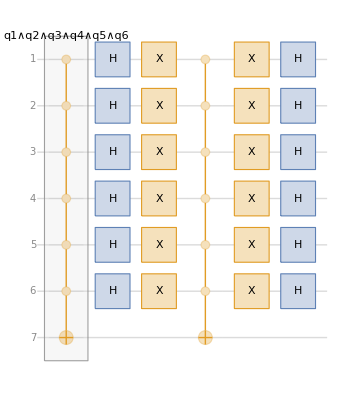

```mathematica
g=QuantumCircuitOperator[{"Grover",f}];
g["Diagram"]
```

初始状态前六个比特是0，最后一个比特是1

```mathematica
QuantumOperator["NOT",{7}]@QuantumState[{"Register",7}]//TraditionalForm
```

0000001

```mathematica
ψ0=QuantumOperator["H",7]@QuantumOperator["NOT",{7}]@QuantumState[{"Register",7}];
```

作用Grover迭代20次

```mathematica
steps=Rest@NestList[g,ψ0,20];
```

```mathematica
success=Normal[QuantumState[{"Register",6,2^6-1}]["Dagger"][QuantumPartialTrace[#,{7}]][[1,1]]][[1]]&/@steps;
```

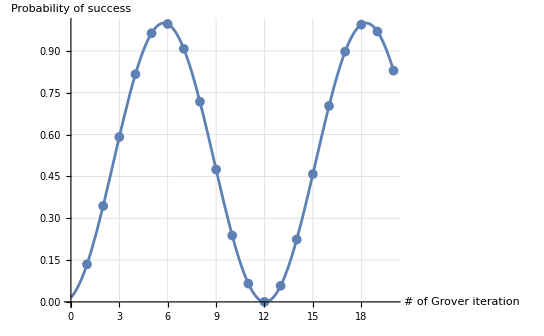

```mathematica
Block[{m,n},m=1;(*解的数量*)n=2^6;(*搜索空间的大小*)Plot[Sin[(2k+1)ArcCos@√(1-m/n)]^2,{k,0,20},PlotLegends->"Expressions"]];
ListPlot[success,GridLines->Automatic,AxesLabel->{"# of Grover iteration","Probability of success" }];
Show[%,%%]
```

#### 辅助比特为

```mathematica
ψ0=QuantumOperator["H",6]@QuantumState[{"Register",7}];
```

applying Grover iteration 20 times

```mathematica
steps=Rest@NestList[g,ψ0,20];
```

```mathematica
success=Normal[QuantumState[{"Register",6,2^6-1}]["Dagger"][QuantumPartialTrace[#,{7}]][[1,1]]][[1]]&/@steps;
```

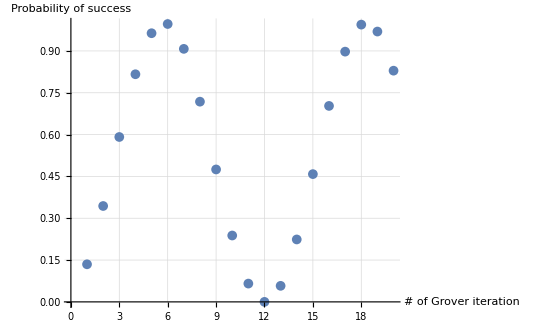

```mathematica
ListPlot[success,GridLines->Automatic,AxesLabel->{"# of Grover iteration","Probability of success" }]
```

### 用相位翻转实现Grover算法

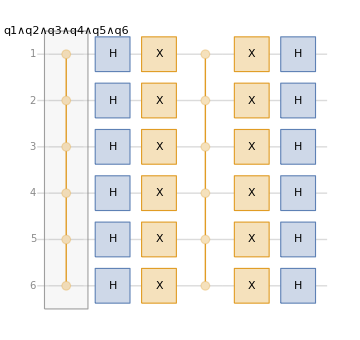

```mathematica
g=QuantumCircuitOperator[{"GroverPhase",f}];
g["Diagram"]
```

```mathematica
QuantumOperator[g["Operators"][[1]]]//TraditionalForm
```

000000000000+000001000001+000010000010+000011000011+000100000100+000101000101+000110000110+000111000111+001000001000+001001001001+001010001010+001011001011+001100001100+001101001101+001110001110+001111001111+010000010000+010001010001+010010010010+010011010011+010100010100+010101010101+010110010110+010111010111+011000011000+011001011001+011010011010+011011011011+011100011100+011101011101+011110011110+011111011111+100000100000+100001100001+100010100010+100011100011+100100100100+100101100101+100110100110+100111100111+101000101000+101001101001+101010101010+101011101011+101100101100+101101101101+101110101110+101111101111+110000110000+110001110001+110010110010+110011110011+110100110100+110101110101+110110110110+110111110111+111000111000+111001111001+111010111010+111011111011+111100111100+111101111101+111110111110-111111111111

the oracle above has the state |111111> as the solution (which is |x=2^6-1>)

Initial state for the circuit (qubit 1-6, each one in |x+>)

```mathematica
ψ0=QuantumOperator["H",6]@QuantumState[{"Register",6}];
```

applying Grover iteration 20 times

```mathematica
steps=NestList[g,ψ0,20];
```

Calculate the success probability after each iteration:

```mathematica
success=Abs[Normal[QuantumState[{"Register",6,2^6-1}]["Dagger"][#][[1,1]]]]^2&/@steps;
```

Plot the success probability:

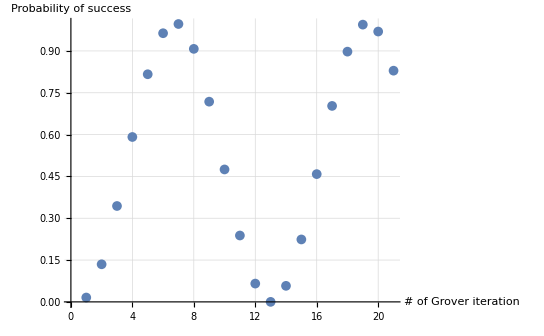

```mathematica
ListPlot[success,GridLines->Automatic,AxesLabel->{"# of Grover iteration","Probability of success" }]
```

## 启发式推导

将搜索问题的目标视为量子控制问题：将初态|ψ 演化到作为解的末态 ，即寻找哈密顿量H，确定时间t，使得尽可能大，甚至使得|ψ =

猜得哈密顿量为

### 用量子模拟方法实现H将导致Grover算法

```mathematica
Ut=E^(I t)MatrixExp[-I KroneckerProduct[{a,b},{a,b}]t].MatrixExp[-I KroneckerProduct[{1,0},{1,0}]t]//FullSimplify[#,a^2+b^2==1]&
```

{{b^2-(-1+b^2) ⅇ^(-ⅈ t),a b (1-ⅇ^(ⅈ t))},{a b (-1+ⅇ^(-ⅈ t)),b^2-(-1+b^2) ⅇ^(ⅈ t)}}

-Graphics-

每经过时间t对应的转角 cos[θ/2]

```mathematica
Clear[n];1/2 Tr[Ut]/.b->1/(√n)//FullSimplify//Expand
```

1/n+Cos[t]-Cos[t]/n

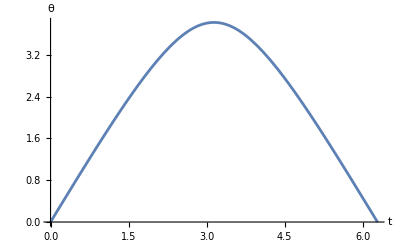

```mathematica
Plot[n=3;2ArcCos[1/n+Cos[t]-Cos[t]/n],{t,0,2π},AxesLabel->{t,θ}]
```

为了使得转角最大，应该令 t = π

因此得到了Grover迭代中的G=HO

## 参考文献和注释

1	Quantum algorithms:
A survey of applications and end-to-end complexities

2	Grover's algorithm: a quantum search algorithm
by Mads Bahrami